```mathematica
ChebyshevT[3, ξ]
```

-3 ξ+4 ξ^3

```mathematica
x=r*Sin[θ]Cos[ϕ]
y=r*Sin[θ]Sin[ϕ]
z=r*Cos[θ]
Simplify[(x-x0)^2+(y-y0)^2+(z-z0)^2==a^2]
Simplify[Solve[(x-x0)^2+(y-y0)^2+(z-z0)^2==a^2, r]]
```

r Cos[ϕ] Sin[θ]

r Sin[θ] Sin[ϕ]

r Cos[θ]

(z0-r Cos[θ])^2+(x0-r Cos[ϕ] Sin[θ])^2+(y0-r Sin[θ] Sin[ϕ])^2==a^2

{{r→1/2 (2 z0 Cos[θ]+y0 Cos[θ-ϕ]-y0 Cos[θ+ϕ]+x0 Sin[θ-ϕ]-2 √(a^2-x0^2-y0^2-z0^2+(z0 Cos[θ]+Sin[θ] (x0 Cos[ϕ]+y0 Sin[ϕ]))^2)+x0 Sin[θ+ϕ])},{r→1/2 (2 z0 Cos[θ]+y0 Cos[θ-ϕ]-y0 Cos[θ+ϕ]+x0 Sin[θ-ϕ]+2 √(a^2-x0^2-y0^2-z0^2+(z0 Cos[θ]+Sin[θ] (x0 Cos[ϕ]+y0 Sin[ϕ]))^2)+x0 Sin[θ+ϕ])}}

```mathematica
FullSimplify[Cos[θ]+√(24+Cos[θ]^2), Assumptions->{0≤θ≤π}]
```

Cos[θ]+√(24+Cos[θ]^2)

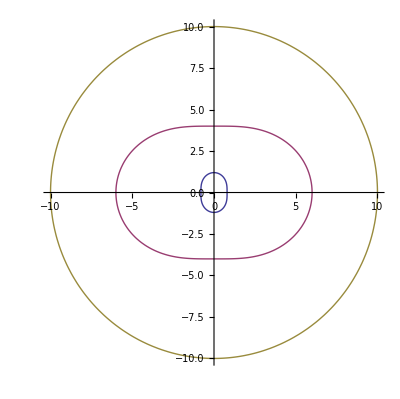

```mathematica
PolarPlot[{1-0.2Cos[2θ], 5+1Cos[2θ], 10}, {θ, -π, π}]
```

```mathematica
SphericalPlot3D[{1-0.2Cos[2θ], 5+1Cos[2θ], 10}, {θ, 0, π}, {ϕ, 1, -1}]
```

-Graphics3D-

```mathematica
plot1=SphericalPlot3D[{1, 3, 5}, {θ, 0, π/2}, {ϕ, 0, 3π/2}, Axes->False, PlotStyle->None, Boxed->False, Mesh->{5, 8}]
```

-Graphics3D-

```mathematica
θi=1;
ϕj=0;
plot2=ParametricPlot3D[{r*Sin[θi]Cos[ϕj], r*Sin[θi]Sin[ϕj], r*Cos[θi]},{r,0,5},
PlotStyle->Directive[Black, Thick]]
```

-Graphics3D-

```mathematica
θi=1;
ϕj=0;
nr=7;
r0[i_]:=Sin[π/2 i/(nr-1)]
r1[i_]:=2-Cos[(π*i)/(nr-1)]
pointtable=N[Table[{r1[i]*Sin[θi]Cos[ϕj], r1[i]*Sin[θi]Sin[ϕj], r1[i]*Cos[θi]},{i,0,nr-1}]];
plot3=ListPointPlot3D[pointtable, PlotStyle->Directive[Red, PointSize[Large]]]
```

-Graphics3D-

```mathematica
Show[plot1, plot2, plot3]
```

-Graphics3D-

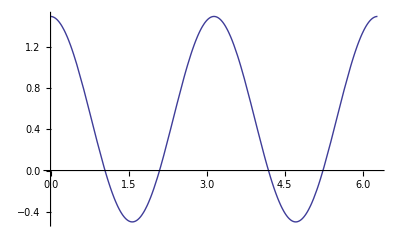

```mathematica
Plot[0.5+Cos[2ϕ], {ϕ, 0, 2π}]
```

## Kernel

```mathematica
Clear[ξ, θ, ϕ];
α0=4;
(*S0[θ_, ϕ_]=Simplify[5(1+0.2(Re[SphericalHarmonicY[2, 1, θ, ϕ]]+Im[SphericalHarmonicY[2, 1, θ, ϕ]])), {θ>0, ϕ>0}];
S0even[θ_, ϕ_]=Simplify[5(1+0.2Re[SphericalHarmonicY[2, 1, θ, ϕ]]), {θ>0, ϕ>0}];
S0odd[θ_, ϕ_]=Simplify[5(0.2Im[SphericalHarmonicY[2, 1, θ, ϕ]]), {θ>0, ϕ>0}];
F0[θ_, ϕ_]:=S0odd[θ, ϕ]/α0-1;
G0[θ_, ϕ_]:=S0even[θ, ϕ]/α0-1;
Simplify[F0[θ, ϕ]]
Simplify[G0[θ, ϕ]]*)
F0[θ_, ϕ_]:=0
(*G0[θ_, ϕ_]:=1/4(1+Cos[θ])*)
G0[θ_, ϕ_]:=1/4(1+Cos[2θ])
A0[ξ_]:=3*ξ^4-2*ξ^6
B0[ξ_]:=1/2(5*ξ^3-3*ξ^5)
```

```mathematica
r[ξ_, θ_, ϕ_]:=α0*(ξ+A0[ξ]*F0[θ, ϕ]+B0[ξ]*G0[θ, ϕ])
R=10;
s[ξ_, θ_, ϕ_]:=R-r[ξ, θ, ϕ]^2/R
f[ξ_, θ_, ϕ_]:=(R*r[ξ, θ, ϕ]^2)/6-r[ξ, θ, ϕ]^4/(20*R)-3/4 R^3
```

```mathematica
Expand[TrigReduce[r[ξ, θ, ϕ]^2]]
Expand[TrigReduce[r[ξ, θ, ϕ]Cos[θ]]]
Simplify[Expand[TrigReduce[r[ξ, θ, ϕ]Cos[θ]]]-r[ξ, θ, ϕ]Cos[θ]]
Expand[TrigReduce[s[ξ, θ, ϕ]]]
Expand[TrigReduce[f[ξ, θ, ϕ]]]
```

16 ξ^2+20 ξ^4-(21 ξ^6)/8-(45 ξ^8)/4+(27 ξ^10)/8+20 ξ^4 Cos[2 θ]+1/2 ξ^6 Cos[2 θ]-15 ξ^8 Cos[2 θ]+9/2 ξ^10 Cos[2 θ]+25/8 ξ^6 Cos[4 θ]-15/4 ξ^8 Cos[4 θ]+9/8 ξ^10 Cos[4 θ]

4 ξ Cos[θ]+15/4 ξ^3 Cos[θ]-9/4 ξ^5 Cos[θ]+5/4 ξ^3 Cos[3 θ]-3/4 ξ^5 Cos[3 θ]

0

10-(8 ξ^2)/5-2 ξ^4+(21 ξ^6)/80+(9 ξ^8)/8-(27 ξ^10)/80-2 ξ^4 Cos[2 θ]-1/20 ξ^6 Cos[2 θ]+3/2 ξ^8 Cos[2 θ]-9/20 ξ^10 Cos[2 θ]-5/16 ξ^6 Cos[4 θ]+3/8 ξ^8 Cos[4 θ]-9/80 ξ^10 Cos[4 θ]

-750+(80 ξ^2)/3+(2404 ξ^4)/75-(303 ξ^6)/40-(2133 ξ^8)/100+(79 ξ^10)/10+(80653 ξ^12)/25600-(339 ξ^14)/256-(2997 ξ^16)/2560+(189 ξ^18)/256-(567 ξ^20)/5120+100/3 ξ^4 Cos[2 θ]-71/30 ξ^6 Cos[2 θ]-727/25 ξ^8 Cos[2 θ]+801/80 ξ^10 Cos[2 θ]+(15713 ξ^12 Cos[2 θ])/3200-57/32 ξ^14 Cos[2 θ]-621/320 ξ^16 Cos[2 θ]+189/160 ξ^18 Cos[2 θ]-(567 ξ^20 Cos[2 θ])/3200+125/24 ξ^6 Cos[4 θ]-31/4 ξ^8 Cos[4 θ]+9/5 ξ^10 Cos[4 θ]+(13769 ξ^12 Cos[4 θ])/6400-123/320 ξ^14 Cos[4 θ]-(3429 ξ^16 Cos[4 θ])/3200+189/320 ξ^18 Cos[4 θ]-(567 ξ^20 Cos[4 θ])/6400-5/16 ξ^10 Cos[6 θ]+47/128 ξ^12 Cos[6 θ]+21/160 ξ^14 Cos[6 θ]-(567 ξ^16 Cos[6 θ])/1600+27/160 ξ^18 Cos[6 θ]-(81 ξ^20 Cos[6 θ])/3200-(25 ξ^12 Cos[8 θ])/1024+15/256 ξ^14 Cos[8 θ]-27/512 ξ^16 Cos[8 θ]+(27 ξ^18 Cos[8 θ])/1280-(81 ξ^20 Cos[8 θ])/25600

```mathematica
j1[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], ξ];
j2[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], θ]/r[ξ, θ, ϕ];
j3[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], ϕ]/(r[ξ, θ, ϕ]Sin[θ]);
anglapr[ξ_, θ_, ϕ_]=(D[r[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[r[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[r[ξ, θ, ϕ], ϕ,ϕ]);
anglapf[ξ_, θ_, ϕ_]=D[f[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[f[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[f[ξ, θ, ϕ], ϕ,ϕ];
```

```mathematica
Expand[TrigReduce[j1[ξ, θ, ϕ]]]
Expand[TrigReduce[j2[ξ, θ, ϕ]]]
Expand[TrigReduce[j3[ξ, θ, ϕ]]]
```

4+(15 ξ^2)/2-(15 ξ^4)/2+15/2 ξ^2 Cos[2 θ]-15/2 ξ^4 Cos[2 θ]

(10 ξ^2 Sin[2 θ])/(-8-5 ξ^2+3 ξ^4-5 ξ^2 Cos[2 θ]+3 ξ^4 Cos[2 θ])-(6 ξ^4 Sin[2 θ])/(-8-5 ξ^2+3 ξ^4-5 ξ^2 Cos[2 θ]+3 ξ^4 Cos[2 θ])

0

```mathematica
part1[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ] r[ξ, θ, ϕ]/ξ(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)2/(j1[ξ, θ, ϕ]r[ξ, θ, ϕ])D[f[ξ, θ, ϕ], ξ];
part2[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ]^2(r[ξ, θ, ϕ]/ξ)^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)1/r[ξ, θ, ϕ]^2 anglapf[ξ, θ, ϕ];
part3a[ξ_, θ_, ϕ_]=2(j2[ξ, θ, ϕ]/r[ξ, θ, ϕ] D[f[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(r[ξ, θ, ϕ]Sin[θ])D[f[ξ, θ, ϕ], ϕ,ξ]);
part3b[ξ_, θ_, ϕ_]=(1/r[ξ, θ, ϕ]^2 anglapr[ξ, θ, ϕ] + 1/j1[ξ, θ, ϕ](1/j1[ξ, θ, ϕ](1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)D[r[ξ, θ, ϕ], ξ, ξ]-2(j2[ξ, θ, ϕ]/r[ξ, θ, ϕ] D[r[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(r[ξ, θ, ϕ]Sin[θ])D[r[ξ, θ, ϕ], ϕ,ξ])))D[f[ξ, θ, ϕ], ξ];
residual[ξ_, θ_, ϕ_]=part1[ξ, θ, ϕ]+part2[ξ, θ, ϕ]+(part3a[ξ, θ, ϕ]+part3b[ξ, θ, ϕ])/j1[ξ, θ, ϕ];
```

```mathematica
Limit[residual[ξ, θ, ϕ], ξ->0]
```

0

```mathematica
ScientificForm[N[Limit[residual[1, θ, ϕ], θ->0]], 18]
```

-3.462666666666666×10^1

```mathematica
ScientificForm[N[residual[7.518398074789773844*^-01,1.178097245096172418*^00,1.570796326794896558*^00]], 18]
```

1.963573842892393

```mathematica
a[ξ_, θ_, ϕ_]:=α^2/j1[ξ, θ, ϕ]^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)
```

```mathematica
tildelapf[ξ_, θ_, ϕ_]=1/α^2(D[f[ξ, θ, ϕ], ξ,ξ]+2/ξ D[f[ξ, θ, ϕ], ξ]+1/ξ^2 anglapf[ξ, θ, ϕ]);
```

```mathematica
pseudospherical[ξ_, θ_, ϕ_]:=a[ξ, θ, ϕ]tildelapf[ξ, θ, ϕ]-residual[ξ, θ, ϕ]
```

```mathematica
pseudospherical[0.8, 2, 2]
```

```mathematica
f[r_, θ_, ϕ_]:=r^2*(r^2-1)Sin[θ]Cos[θ](Cos[ϕ]+Sin[ϕ])
```

```mathematica
lapf[ξ_, θ_, ϕ_]=(D[f[r, θ, ϕ], r,r]+2/r D[f[r, θ, ϕ], r]+1/r^2(D[f[r, θ, ϕ], θ,θ]+1/Tan[θ] D[f[r, θ, ϕ], θ]+1/Sin[θ]^2 D[f[r, θ, ϕ], ϕ,ϕ]))/.r->r[ξ, θ, ϕ];
```

```mathematica
lapf[0.8, 2, 2]
```

## Shell

```mathematica
Clear[ξ, θ, ϕ]
(*α=3/2;
β=5/2;
F[θ_, ϕ_]:=0;
G[θ_, ϕ_]:=2/3(1+Cos[θ]);*)
α=2;
β=8;
F[θ_, ϕ_]:=1/2(-1+Cos[θ]);
G[θ_, ϕ_]:=0;
A[ξ_]:=1/4(ξ^3-3*ξ+2)
B[ξ_]:=1/4(-ξ^3+3*ξ+2)
```

```mathematica
r[ξ_, θ_, ϕ_]:=α*(ξ+A[ξ]*F[θ, ϕ]+B[ξ]*G[θ, ϕ])+β
R=10;
s[ξ_, θ_, ϕ_]:=1
f[ξ_, θ_, ϕ_]:=-R^2/2+r[ξ, θ, ϕ]^2/6
(*s[ξ_, θ_, ϕ_]:=R-r[ξ, θ, ϕ]^2/B
f[ξ_, θ_, ϕ_]:=(R*r[ξ, θ, ϕ]^2)/6-r[ξ, θ, ϕ]^4/(20*R)-3/4 R^3*)
```

```mathematica
Expand[TrigReduce[r[ξ, θ, ϕ]]]
Expand[TrigReduce[r[ξ, θ, ϕ]Cos[θ]]]
Expand[TrigReduce[s[ξ, θ, ϕ]]]
Expand[TrigReduce[f[ξ, θ, ϕ]]]
```

15/2+(11 ξ)/4-ξ^3/4+Cos[θ]/2-3/4 ξ Cos[θ]+1/4 ξ^3 Cos[θ]

1/4-(3 ξ)/8+ξ^3/8+(15 Cos[θ])/2+11/4 ξ Cos[θ]-1/4 ξ^3 Cos[θ]+1/4 Cos[2 θ]-3/8 ξ Cos[2 θ]+1/8 ξ^3 Cos[2 θ]

1

-1949/48+(109 ξ)/16+(251 ξ^2)/192-(29 ξ^3)/48-(25 ξ^4)/96+ξ^6/64+(5 Cos[θ])/4-17/12 ξ Cos[θ]-11/16 ξ^2 Cos[θ]+7/12 ξ^3 Cos[θ]+7/24 ξ^4 Cos[θ]-1/48 ξ^6 Cos[θ]+1/48 Cos[2 θ]-1/16 ξ Cos[2 θ]+3/64 ξ^2 Cos[2 θ]+1/48 ξ^3 Cos[2 θ]-1/32 ξ^4 Cos[2 θ]+1/192 ξ^6 Cos[2 θ]

```mathematica
j1[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], ξ];
j2[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], θ]/r[ξ, θ, ϕ];
j3[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], ϕ]/(r[ξ, θ, ϕ]Sin[θ]);
anglapr[ξ_, θ_, ϕ_]=(D[r[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[r[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[r[ξ, θ, ϕ], ϕ,ϕ]);
anglapf[ξ_, θ_, ϕ_]=D[f[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[f[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[f[ξ, θ, ϕ], ϕ,ϕ];
```

```mathematica
part1[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ] r[ξ, θ, ϕ]/(ξ+β/α)(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)2/(j1[ξ, θ, ϕ]r[ξ, θ, ϕ])D[f[ξ, θ, ϕ], ξ];
part2[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ]^2(r[ξ, θ, ϕ]/(ξ+β/α))^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)1/r[ξ, θ, ϕ]^2 anglapf[ξ, θ, ϕ];
part3a[ξ_, θ_, ϕ_]=2(j2[ξ, θ, ϕ]/r[ξ, θ, ϕ] D[f[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(r[ξ, θ, ϕ]Sin[θ])D[f[ξ, θ, ϕ], ϕ,ξ]);
part3b[ξ_, θ_, ϕ_]=(1/r[ξ, θ, ϕ]^2 anglapr[ξ, θ, ϕ] + 1/j1[ξ, θ, ϕ](1/j1[ξ, θ, ϕ](1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)D[r[ξ, θ, ϕ], ξ, ξ]-2(j2[ξ, θ, ϕ]/r[ξ, θ, ϕ] D[r[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(r[ξ, θ, ϕ]Sin[θ])D[r[ξ, θ, ϕ], ϕ,ξ])))D[f[ξ, θ, ϕ], ξ];
residual[ξ_, θ_, ϕ_]:=part1[ξ, θ, ϕ]+part2[ξ, θ, ϕ]+(part3a[ξ, θ, ϕ]+part3b[ξ, θ, ϕ])/j1[ξ, θ, ϕ];
```

```mathematica
a[ξ_, θ_, ϕ_]:=α^2/j1[ξ, θ, ϕ]^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)
seff[ξ_, θ_, ϕ_]:=(s[ξ, θ, ϕ]+residual[ξ, θ, ϕ])/a[ξ, θ, ϕ]
```

```mathematica
Simplify[Expand[residual[ξ, θ, ϕ]]]
Simplify[Expand[a[ξ, θ, ϕ]]]
```

-(9349568+29370336 ξ+25882964 ξ^2+8917052 ξ^3+1507441 ξ^4+1264220 ξ^5+727324 ξ^6-47588 ξ^7-144922 ξ^8-32156 ξ^9+3832 ξ^10+1800 ξ^11+129 ξ^12-8 (1127144+3684952 ξ+3364654 ξ^2+1061720 ξ^3+76997 ξ^4+178246 ξ^5+142741 ξ^6-1252 ξ^7-28835 ξ^8-7522 ξ^9+685 ξ^10+432 ξ^11+38 ξ^12) Cos[θ]+4 (-1+ξ)^2 (164064+176384 ξ+225100 ξ^2+220436 ξ^3+46353 ξ^4-64670 ξ^5-43837 ξ^6-6768 ξ^7+2071 ξ^8+794 ξ^9+73 ξ^10) Cos[2 θ]-24 (-1+ξ)^4 (-2424-6952 ξ-9418 ξ^2-6656 ξ^3-2059 ξ^4+146 ξ^5+285 ξ^6+72 ξ^7+6 ξ^8) Cos[3 θ]+1728 Cos[4 θ]-4320 ξ Cos[4 θ]-2052 ξ^2 Cos[4 θ]+11988 ξ^3 Cos[4 θ]-2565 ξ^4 Cos[4 θ]-12204 ξ^5 Cos[4 θ]+4644 ξ^6 Cos[4 θ]+5940 ξ^7 Cos[4 θ]-1998 ξ^8 Cos[4 θ]-1620 ξ^9 Cos[4 θ]+216 ξ^10 Cos[4 θ]+216 ξ^11 Cos[4 θ]+27 ξ^12 Cos[4 θ])/(24 (4+ξ)^2 (330+121 ξ-90 ξ^2-44 ξ^3+3 ξ^5+(-68-66 ξ+84 ξ^2+56 ξ^3-6 ξ^5) Cos[θ]+3 (-1+ξ)^3 (2+3 ξ+ξ^2) Cos[θ]^2)^2)

-(128 (-452-324 ξ-65 ξ^2+28 ξ^3+14 ξ^4-ξ^6+(-1+ξ)^2 (-60-52 ξ-11 ξ^2+2 ξ^3+ξ^4) Cos[θ]))/((330+121 ξ-90 ξ^2-44 ξ^3+3 ξ^5+(-68-66 ξ+84 ξ^2+56 ξ^3-6 ξ^5) Cos[θ]+3 (-1+ξ)^3 (2+3 ξ+ξ^2) Cos[θ]^2)^2)

```mathematica
Simplify[Expand[seff[ξ, θ, ϕ]]]
(*Expand[N[Series[Simplify[Expand[seff[ξ, θ, ϕ]]], {ξ, 0, 15}]]]*)
```

1/(192 (4+ξ)^2)(4622-116 ξ-4116 ξ^2-1950 ξ^3+113 ξ^4+216 ξ^5+31 ξ^6-4 (430-408 ξ-1143 ξ^2-518 ξ^3+57 ξ^4+72 ξ^5+10 ξ^6) Cos[θ]+3 (-1+ξ)^2 (14+88 ξ+90 ξ^2+30 ξ^3+3 ξ^4) Cos[2 θ])

```mathematica
chebcoeff[n_]:=Expand[Integrate[2/(π*(1+KroneckerDelta[0, n]))(Simplify[seff[ξ,θ,ϕ]]*ChebyshevT[n, ξ])/(√(1-ξ^2)), {ξ, -1, 1}]]
```

```mathematica
(chebcoefftable=Table[N[chebcoeff[n], 18], {n, 0, 10}])//TableForm
```

1.03501464246415-0.0663271545336032939 Cos[θ]-0.017858780650708646 Cos[2. θ]
-0.83479018329602687+0.853476077266801647 Cos[θ]+0.0413511144571877 Cos[2. θ]
-0.45302138656413438+0.471974962948991046 Cos[θ]-0.025907058368232533 Cos[2. θ]
-0.014100759659515178+0.0129723610157383214 Cos[θ]-0.0032807539171786902 Cos[2. θ]
0.0164550239265752172-0.0214932580868419485 Cos[θ]+0.0055982699646203031 Cos[2. θ]
0.000502123024975194514-0.000692515433249751733 Cos[θ]+0.000119258534401528769 Cos[2. θ]
-0.000067423103856892757+0.00010254146276044006 Cos[θ]-0.0000260831722728915735 Cos[2. θ]
9.02684765914838837×10^-6-0.000014876435950572132 Cos[θ]+4.7019691192063696×10^-6 Cos[2. θ]
-1.2053675031150562×10^-6+2.12478519141982177×10^-6 Cos[θ]-7.7365094122150054×10^-7 Cos[2. θ]
1.6057128113685801×10^-7-2.9976124224562921×10^-7 Cos[θ]+1.206751566600251×10^-7 Cos[2. θ]
-2.134398207747631×10^-8+4.18696909358856646×10^-8 Cos[θ]-1.8174020351705594×10^-8 Cos[2. θ]

```mathematica
rbyxiplusbbya[ξ_, θ_, ϕ_]=r[ξ, θ, ϕ]/(ξ+β/α);
dfdxi[ξ_, θ_, ϕ_]=D[f[ξ, θ, ϕ], ξ];
onebyrdfdxi[ξ_, θ_, ϕ_]=1/r[ξ, θ, ϕ] D[f[ξ, θ, ϕ], ξ];
d2rdxi2[ξ_, θ_, ϕ_]=D[r[ξ, θ, ϕ], ξ, ξ];
onebyrd2fdthetadxi[ξ_, θ_, ϕ_]=1/r[ξ, θ, ϕ] D[f[ξ, θ, ϕ], θ,ξ];
onebyrd2rdthetadxi[ξ_, θ_, ϕ_]=1/r[ξ, θ, ϕ] D[r[ξ, θ, ϕ], θ,ξ];
onebyrsinthetad2fdphidxi[ξ_, θ_, ϕ_]=1/(r[ξ, θ, ϕ]Sin[θ])D[f[ξ, θ, ϕ], ϕ,ξ];
onebyrsinthetad2rdphidxi[ξ_, θ_, ϕ_]=1/(r[ξ, θ, ϕ]Sin[θ])D[r[ξ, θ, ϕ], ϕ,ξ];
onebyrsqanglaplacef[ξ_, θ_, ϕ_]=1/r[ξ, θ, ϕ]^2 anglapf[ξ, θ, ϕ];
onebyrsqanglaplacer[ξ_, θ_, ϕ_]=1/r[ξ, θ, ϕ]^2 anglapr[ξ, θ, ϕ];
```

```mathematica
nr=15;
nt=7;
np=12;
i=14;
j=6;
k=11;
ξ=N[-Cos[(π*i)/(nr-1)]];
θ=N[(π*j)/(nt-1)];
ϕ=N[(2*π*k)/np];
```

```mathematica
ScientificForm[j1[ξ, θ, ϕ], 18]
ScientificForm[j2[ξ, θ, ϕ], 18]
ScientificForm[j3[ξ, θ, ϕ], 18]
ScientificForm[rbyxiplusbbya[ξ, θ, ϕ], 18]
ScientificForm[dfdxi[ξ, θ, ϕ], 18]
ScientificForm[onebyrdfdxi[ξ, θ, ϕ], 18]
ScientificForm[d2rdxi2[ξ, θ, ϕ], 18]
ScientificForm[onebyrd2fdthetadxi[ξ, θ, ϕ], 18]
ScientificForm[onebyrd2rdthetadxi[ξ, θ, ϕ], 18]
ScientificForm[onebyrsinthetad2fdphidxi[ξ, θ, ϕ], 18]
ScientificForm[onebyrsinthetad2rdphidxi[ξ, θ, ϕ], 18]
ScientificForm[onebyrsqanglaplacef[ξ, θ, ϕ], 18]
ScientificForm[onebyrsqanglaplacer[ξ, θ, ϕ], 18]
ScientificForm[residual[ξ, θ, ϕ], 18]
```

2.

0.

0

2.

6.666666666666666

6.666666666666666×10^-1

-3.

0.

0.

0

0

0.

0.

-2.5

```mathematica
ScientificForm[r[ξ, θ, ϕ], 18]
ScientificForm[a[ξ, θ, ϕ], 18]
ScientificForm[part1[ξ, θ, ϕ], 18]
ScientificForm[part2[ξ, θ, ϕ], 18]
ScientificForm[part3a[ξ, θ, ϕ], 18]
ScientificForm[part3b[ξ, θ, ϕ], 18]
ScientificForm[residual[ξ, θ, ϕ], 18]
ScientificForm[s[ξ, θ, ϕ], 18]
ScientificForm[seff[ξ, θ, ϕ], 18]
```

1.×10^1

1.

0.

0.

0.

-5.

-2.5

1

-1.5

```mathematica
tildelapf[ξ_, θ_, ϕ_]=1/α^2(D[f[ξ, θ, ϕ], ξ,ξ]+2/(ξ+β/α)D[f[ξ, θ, ϕ], ξ]+1/(ξ+β/α)^2 anglapf[ξ, θ, ϕ]);
```

```mathematica
tildelapf[-.8, 2, 2]
```

1.84712

```mathematica
pseudospherical[ξ_, θ_, ϕ_]:=a[ξ, θ, ϕ]tildelapf[ξ, θ, ϕ]-residual[ξ, θ, ϕ]
```

```mathematica
pseudospherical[-.8, 2, 2]
```

1.

```mathematica
f[r_, θ_, ϕ_]:=r^2(r^2-1)(3 Cos[θ]^2-1);
```

```mathematica
lapf[ξ_, θ_, ϕ_]=(D[f[r, θ, ϕ], r,r]+2/r D[f[r, θ, ϕ], r]+1/r^2(D[f[r, θ, ϕ], θ,θ]+1/Tan[θ] D[f[r, θ, ϕ], θ]+1/Sin[θ]^2 D[f[r, θ, ϕ], ϕ,ϕ]))/.r->r[ξ, θ, ϕ]
```

2 (-1+(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2) (-1+3 Cos[θ]^2)+10 (8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2 (-1+3 Cos[θ]^2)+(2 (2 (-1+(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2) (8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ]))) (-1+3 Cos[θ]^2)+2 (8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^3 (-1+3 Cos[θ]^2)))/(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))+(-12 (-1+(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2) (8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2 Cos[θ]^2+6 (-1+(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2) (8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2 Sin[θ]^2)/(8+2 (ξ+1/8 (2-3 ξ+ξ^3) (-1+Cos[θ])))^2

```mathematica
lapf[-.8, 2, 2]
```

-169.748

## External Domain

```mathematica
α=-0.02;
Szm1[θ_, ϕ_]:=Simplify[10(1+0.2(Re[SphericalHarmonicY[2, 1, θ, ϕ]]+Im[SphericalHarmonicY[2, 1, θ, ϕ]])), {θ>0, ϕ>0}]
F[θ_, ϕ_]:=1/(α*Szm1[θ, ϕ])+2;
Simplify[F[θ, ϕ]]
A[ξ_]:=1/4(ξ^3-3*ξ+2)
```

2-50./(10.+Cos[θ] Sin[θ]^3 (-2.50334 Cos[3 ϕ]-2.50334 Sin[3 ϕ]))

```mathematica
u[ξ_, θ_, ϕ_]:=α*(ξ+A[ξ]*F[θ, ϕ]-1)
f[ξ_, θ_, ϕ_]:=u[ξ, θ, ϕ]^2(u[ξ, θ, ϕ]^2-1)Sin[θ]Cos[θ](Cos[ϕ]+Sin[ϕ]);
(*f[ξ_, θ_, ϕ_]:=ξ^2(ξ^2-1)Sin[θ]Cos[θ](Cos[ϕ]+Sin[ϕ]);*)
```

```mathematica
j1[ξ_, θ_, ϕ_]=D[u[ξ, θ, ϕ], ξ];
j2[ξ_, θ_, ϕ_]=D[u[ξ, θ, ϕ], θ]/u[ξ, θ, ϕ];
j3[ξ_, θ_, ϕ_]=D[u[ξ, θ, ϕ], ϕ]/(u[ξ, θ, ϕ]Sin[θ]);
anglapu[ξ_, θ_, ϕ_]=(D[u[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[u[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[u[ξ, θ, ϕ], ϕ,ϕ]);
anglapf[ξ_, θ_, ϕ_]=D[f[ξ, θ, ϕ], θ,θ]+1/Tan[θ] D[f[ξ, θ, ϕ], θ]+1/Sin[θ]^2 D[f[ξ, θ, ϕ], ϕ,ϕ];
```

```mathematica
part1[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ] u[ξ, θ, ϕ]/(ξ-1)(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)2/(j1[ξ, θ, ϕ]u[ξ, θ, ϕ])D[f[ξ, θ, ϕ], ξ];
part2[ξ_, θ_, ϕ_]=(1/j1[ξ, θ, ϕ]^2(u[ξ, θ, ϕ]/(ξ-1))^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)-1)1/u[ξ, θ, ϕ]^2 anglapf[ξ, θ, ϕ];
part3a[ξ_, θ_, ϕ_]=2(j2[ξ, θ, ϕ]/u[ξ, θ, ϕ] D[f[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(u[ξ, θ, ϕ]Sin[θ])D[f[ξ, θ, ϕ], ϕ,ξ]);
part3b[ξ_, θ_, ϕ_]=(1/u[ξ, θ, ϕ]^2 anglapu[ξ, θ, ϕ] + 1/j1[ξ, θ, ϕ](1/j1[ξ, θ, ϕ](1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)D[u[ξ, θ, ϕ], ξ, ξ]-2(j2[ξ, θ, ϕ]/u[ξ, θ, ϕ] D[u[ξ, θ, ϕ], θ,ξ]+j3[ξ, θ, ϕ]/(u[ξ, θ, ϕ]Sin[θ])D[u[ξ, θ, ϕ], ϕ,ξ])))D[f[ξ, θ, ϕ], ξ];
residual[ξ_, θ_, ϕ_]=(*part1[ξ, θ, ϕ]+*)part2[ξ, θ, ϕ]+(part3a[ξ, θ, ϕ]+part3b[ξ, θ, ϕ])/j1[ξ, θ, ϕ];
```

```mathematica
Limit[residual[ξ, θ, ϕ], ξ->1]
```

0.

```mathematica
residual[-.8, 2, 2]
```

-3.41503

```mathematica
a[ξ_, θ_, ϕ_]:=α^2/j1[ξ, θ, ϕ]^2(1+j2[ξ, θ, ϕ]^2+j3[ξ, θ, ϕ]^2)
```

```mathematica
a[-.8, 2, 2]
```

0.321531

```mathematica
tildelapf[ξ_, θ_, ϕ_]=1/α^2(D[f[ξ, θ, ϕ], ξ,ξ]+1/(ξ-1)^2 anglapf[ξ, θ, ϕ]);
```

```mathematica
tildelapf[-.8, 2, 2]
```

-12.9719

```mathematica
pseudospherical[ξ_, θ_, ϕ_]:=a[ξ, θ, ϕ]tildelapf[ξ, θ, ϕ]-residual[ξ, θ, ϕ]
```

```mathematica
pseudospherical[-.8, 2, 2]
```

-0.755829

```mathematica
f[u_, θ_, ϕ_]:=u^2(u^2-1)Sin[θ]Cos[θ](Cos[ϕ]+Sin[ϕ]);
```

```mathematica
lapfbyu4[ξ_, θ_, ϕ_]=(D[f[u, θ, ϕ], u,u]+1/u^2(D[f[u, θ, ϕ], θ,θ]+1/Tan[θ] D[f[u, θ, ϕ], θ]+1/Sin[θ]^2 D[f[u, θ, ϕ], ϕ,ϕ]))/.u->u[ξ, θ, ϕ];
```

```mathematica
u[-.8, 2, 2]
```

0.091596

```mathematica
lapfbyu4[-.8, 2, 2]
```

-0.755829

## Evaluate Laplacian

```mathematica
(*(metric={{1, 0, 0}, {0, 1, 0}, { 0, 0, 1}})//MatrixForm*)
(*(metric={{1, 0, 0}, {0, ξ^2, 0}, { 0, 0, ξ^2 Sin[θ]^2}})//MatrixForm*)
(metric={{(D[R[ξ, θ, ϕ], ξ])^2, D[R[ξ, θ, ϕ], ξ]D[R[ξ, θ, ϕ], θ], D[R[ξ, θ, ϕ], ξ]D[R[ξ, θ, ϕ], ϕ]}, {D[R[ξ, θ, ϕ], ξ]D[R[ξ, θ, ϕ], θ], R[ξ, θ, ϕ]^2+(D[R[ξ, θ, ϕ], θ])^2, D[R[ξ, θ, ϕ], θ]D[R[ξ, θ, ϕ], ϕ]}, { D[R[ξ, θ, ϕ], ξ]D[R[ξ, θ, ϕ], ϕ], D[R[ξ, θ, ϕ], θ]D[R[ξ, θ, ϕ], ϕ], R[ξ, θ, ϕ]^2 Sin[θ]^2+(D[R[ξ, θ, ϕ], ϕ])^2}})//MatrixForm
```

((R^(1,0,0)[ξ,θ,ϕ])^2 | R^(0,1,0)[ξ,θ,ϕ] R^(1,0,0)[ξ,θ,ϕ] | R^(0,0,1)[ξ,θ,ϕ] R^(1,0,0)[ξ,θ,ϕ]
R^(0,1,0)[ξ,θ,ϕ] R^(1,0,0)[ξ,θ,ϕ] | R[ξ,θ,ϕ]^2+(R^(0,1,0)[ξ,θ,ϕ])^2 | R^(0,0,1)[ξ,θ,ϕ] R^(0,1,0)[ξ,θ,ϕ]
R^(0,0,1)[ξ,θ,ϕ] R^(1,0,0)[ξ,θ,ϕ] | R^(0,0,1)[ξ,θ,ϕ] R^(0,1,0)[ξ,θ,ϕ] | R[ξ,θ,ϕ]^2 Sin[θ]^2+(R^(0,0,1)[ξ,θ,ϕ])^2)

```mathematica
(*rootmetric=Simplify[√Det[metric], Assumptions->0<θ<π&&ξ>0]*)
rootmetric=Simplify[√Det[metric], Assumptions->0<θ<π&&R[ξ, θ, ϕ]>0&&Derivative[1,0,0][R][ξ,θ,ϕ]>0]
```

R[ξ,θ,ϕ]^2 Sin[θ] R^(1,0,0)[ξ,θ,ϕ]

```mathematica
(invmetric=Inverse[metric])//MatrixForm
```

((Csc[θ]^2 (R[ξ,θ,ϕ]^4 Sin[θ]^2+R[ξ,θ,ϕ]^2 (R^(0,0,1)[ξ,θ,ϕ])^2+R[ξ,θ,ϕ]^2 Sin[θ]^2 (R^(0,1,0)[ξ,θ,ϕ])^2))/(R[ξ,θ,ϕ]^4 (R^(1,0,0)[ξ,θ,ϕ])^2) | -(R^(0,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]) | -(Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])
-(R^(0,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]) | 1/R[ξ,θ,ϕ]^2 | 0
-(Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]) | 0 | Csc[θ]^2/R[ξ,θ,ϕ]^2)

```mathematica
partialf={D[f[ξ, θ, ϕ], ξ], D[f[ξ, θ, ϕ], θ], D[f[ξ, θ, ϕ], ϕ]}
```

{f^(1,0,0)[ξ,θ,ϕ],f^(0,1,0)[ξ,θ,ϕ],f^(0,0,1)[ξ,θ,ϕ]}

```mathematica
gijpartialjf=Table[Sum[invmetric⟦i, j⟧*gradf⟦j⟧, {j, 1, 3}], {i, 1, 3}]
```

{(Csc[θ]^2 (R[ξ,θ,ϕ]^4 Sin[θ]^2+R[ξ,θ,ϕ]^2 (R^(0,0,1)[ξ,θ,ϕ])^2+R[ξ,θ,ϕ]^2 Sin[θ]^2 (R^(0,1,0)[ξ,θ,ϕ])^2) f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^4 (R^(1,0,0)[ξ,θ,ϕ])^2)-(Csc[θ]^2 f^(0,0,1)[ξ,θ,ϕ] R^(0,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])-(f^(0,1,0)[ξ,θ,ϕ] R^(0,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]),(f^(0,1,0)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2-(R^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]),(Csc[θ]^2 f^(0,0,1)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2-(Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])}

```mathematica
Expand[gijpartialjf]
```

{(f^(1,0,0)[ξ,θ,ϕ])/((R^(1,0,0)[ξ,θ,ϕ])^2)+(Csc[θ]^2 (R^(0,0,1)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)+((R^(0,1,0)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)-(Csc[θ]^2 f^(0,0,1)[ξ,θ,ϕ] R^(0,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])-(f^(0,1,0)[ξ,θ,ϕ] R^(0,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]),(f^(0,1,0)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2-(R^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ]),(Csc[θ]^2 f^(0,0,1)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2-(Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])}

```mathematica
laplacian=1/rootmetric(D[(rootmetric*gijpartialjf⟦1⟧), ξ]+ D[(rootmetric*gijpartialjf⟦2⟧), θ]+ D[(rootmetric*gijpartialjf⟦3⟧), ϕ]);
```

```mathematica
Expand[laplacian]
```

(Csc[θ]^2 f^(0,0,2)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2+(Cot[θ] f^(0,1,0)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2+(f^(0,2,0)[ξ,θ,ϕ])/R[ξ,θ,ϕ]^2+(2 f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ] R^(1,0,0)[ξ,θ,ϕ])-(Csc[θ]^2 R^(0,0,2)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])-(Cot[θ] R^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])-(R^(0,2,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])-(2 Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ] f^(1,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])+(2 Csc[θ]^2 R^(0,0,1)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ] R^(1,0,1)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)-(2 R^(0,1,0)[ξ,θ,ϕ] f^(1,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 R^(1,0,0)[ξ,θ,ϕ])+(2 R^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ] R^(1,1,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)+(f^(2,0,0)[ξ,θ,ϕ])/((R^(1,0,0)[ξ,θ,ϕ])^2)+(Csc[θ]^2 (R^(0,0,1)[ξ,θ,ϕ])^2 f^(2,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)+((R^(0,1,0)[ξ,θ,ϕ])^2 f^(2,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^2)-(f^(1,0,0)[ξ,θ,ϕ] R^(2,0,0)[ξ,θ,ϕ])/((R^(1,0,0)[ξ,θ,ϕ])^3)-(Csc[θ]^2 (R^(0,0,1)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ] R^(2,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^3)-((R^(0,1,0)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ] R^(2,0,0)[ξ,θ,ϕ])/(R[ξ,θ,ϕ]^2 (R^(1,0,0)[ξ,θ,ϕ])^3)

## Evaluate Laplacian in external domain

```mathematica
(metric=U[ξ, θ, ϕ]^-4{{(D[U[ξ, θ, ϕ], ξ])^2, D[U[ξ, θ, ϕ], ξ]D[U[ξ, θ, ϕ], θ], D[U[ξ, θ, ϕ], ξ]D[U[ξ, θ, ϕ], ϕ]}, {D[U[ξ, θ, ϕ], ξ]D[U[ξ, θ, ϕ], θ], U[ξ, θ, ϕ]^2+(D[U[ξ, θ, ϕ], θ])^2, D[U[ξ, θ, ϕ], θ]D[U[ξ, θ, ϕ], ϕ]}, { D[U[ξ, θ, ϕ], ξ]D[U[ξ, θ, ϕ], ϕ], D[U[ξ, θ, ϕ], θ]D[U[ξ, θ, ϕ], ϕ], U[ξ, θ, ϕ]^2 Sin[θ]^2+(D[U[ξ, θ, ϕ], ϕ])^2}})//MatrixForm
```

(((U^(1,0,0)[ξ,θ,ϕ])^2)/U[ξ,θ,ϕ]^4 | (U^(0,1,0)[ξ,θ,ϕ] U^(1,0,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4 | (U^(0,0,1)[ξ,θ,ϕ] U^(1,0,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4
(U^(0,1,0)[ξ,θ,ϕ] U^(1,0,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4 | (U[ξ,θ,ϕ]^2+(U^(0,1,0)[ξ,θ,ϕ])^2)/U[ξ,θ,ϕ]^4 | (U^(0,0,1)[ξ,θ,ϕ] U^(0,1,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4
(U^(0,0,1)[ξ,θ,ϕ] U^(1,0,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4 | (U^(0,0,1)[ξ,θ,ϕ] U^(0,1,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4 | (Sin[θ]^2 U[ξ,θ,ϕ]^2+(U^(0,0,1)[ξ,θ,ϕ])^2)/U[ξ,θ,ϕ]^4)

```mathematica
rootmetric=Simplify[√Det[metric], Assumptions->0<θ<π&&U[ξ, θ, ϕ]>0&&Derivative[1,0,0][U][ξ,θ,ϕ]>0]
```

(Sin[θ] U^(1,0,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^4

```mathematica
(invmetric=Inverse[metric])//MatrixForm
```

((Csc[θ]^2 U[ξ,θ,ϕ]^8 (Sin[θ]^2/U[ξ,θ,ϕ]^4+((U^(0,0,1)[ξ,θ,ϕ])^2)/U[ξ,θ,ϕ]^6+(Sin[θ]^2 (U^(0,1,0)[ξ,θ,ϕ])^2)/U[ξ,θ,ϕ]^6))/((U^(1,0,0)[ξ,θ,ϕ])^2) | -(U[ξ,θ,ϕ]^2 U^(0,1,0)[ξ,θ,ϕ])/(U^(1,0,0)[ξ,θ,ϕ]) | -(Csc[θ]^2 U[ξ,θ,ϕ]^2 U^(0,0,1)[ξ,θ,ϕ])/(U^(1,0,0)[ξ,θ,ϕ])
-(U[ξ,θ,ϕ]^2 U^(0,1,0)[ξ,θ,ϕ])/(U^(1,0,0)[ξ,θ,ϕ]) | U[ξ,θ,ϕ]^2 | 0
-(Csc[θ]^2 U[ξ,θ,ϕ]^2 U^(0,0,1)[ξ,θ,ϕ])/(U^(1,0,0)[ξ,θ,ϕ]) | 0 | Csc[θ]^2 U[ξ,θ,ϕ]^2)

```mathematica
partialf={D[f[ξ, θ, ϕ], ξ], D[f[ξ, θ, ϕ], θ], D[f[ξ, θ, ϕ], ϕ]}
```

{f^(1,0,0)[ξ,θ,ϕ],f^(0,1,0)[ξ,θ,ϕ],f^(0,0,1)[ξ,θ,ϕ]}

```mathematica
gijpartialjf=Table[Sum[invmetric⟦i, j⟧*gradf⟦j⟧, {j, 1, 3}], {i, 1, 3}];
```

```mathematica
laplacian=1/rootmetric(D[(rootmetric*gijpartialjf⟦1⟧), ξ]+ D[(rootmetric*gijpartialjf⟦2⟧), θ]+ D[(rootmetric*gijpartialjf⟦3⟧), ϕ]);
```

```mathematica
Expand[laplacian/U[ξ, θ, ϕ]^4]
```

(Csc[θ]^2 f^(0,0,2)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^2+(Cot[θ] f^(0,1,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^2+(f^(0,2,0)[ξ,θ,ϕ])/U[ξ,θ,ϕ]^2-(Csc[θ]^2 U^(0,0,2)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 U^(1,0,0)[ξ,θ,ϕ])-(Cot[θ] U^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 U^(1,0,0)[ξ,θ,ϕ])-(U^(0,2,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 U^(1,0,0)[ξ,θ,ϕ])-(2 Csc[θ]^2 U^(0,0,1)[ξ,θ,ϕ] f^(1,0,1)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 U^(1,0,0)[ξ,θ,ϕ])+(2 Csc[θ]^2 U^(0,0,1)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ] U^(1,0,1)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^2)-(2 U^(0,1,0)[ξ,θ,ϕ] f^(1,1,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 U^(1,0,0)[ξ,θ,ϕ])+(2 U^(0,1,0)[ξ,θ,ϕ] f^(1,0,0)[ξ,θ,ϕ] U^(1,1,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^2)+(f^(2,0,0)[ξ,θ,ϕ])/((U^(1,0,0)[ξ,θ,ϕ])^2)+(Csc[θ]^2 (U^(0,0,1)[ξ,θ,ϕ])^2 f^(2,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^2)+((U^(0,1,0)[ξ,θ,ϕ])^2 f^(2,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^2)-(f^(1,0,0)[ξ,θ,ϕ] U^(2,0,0)[ξ,θ,ϕ])/((U^(1,0,0)[ξ,θ,ϕ])^3)-(Csc[θ]^2 (U^(0,0,1)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ] U^(2,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^3)-((U^(0,1,0)[ξ,θ,ϕ])^2 f^(1,0,0)[ξ,θ,ϕ] U^(2,0,0)[ξ,θ,ϕ])/(U[ξ,θ,ϕ]^2 (U^(1,0,0)[ξ,θ,ϕ])^3)

## other stuff

```mathematica
i=5;
ChebyshevT[i, x]
Expand[1/(4(i-2)(i-1))D[ChebyshevT[i-2, x], x,x]-1/(2(i-1)(i+1))D[ChebyshevT[i, x], x,x]+1/(4(i+1)(i+2))D[ChebyshevT[i+2, x], x,x]]
```

5 x-20 x^3+16 x^5

5 x-20 x^3+16 x^5

```mathematica
f[x_]=Sum[ChebyshevT[i, x], {i, 0, 4}]
```

1-2 x-6 x^2+4 x^3+8 x^4

```mathematica
D[f[x], x,x]
```

-12+24 x+96 x^2

```mathematica
Expand[56ChebyshevT[0, x]+24ChebyshevT[1, x]+48ChebyshevT[2, x]]
```

8+24 x+96 x^2

```mathematica
a=Table[1, {i, 0, 4}]
```

{1,1,1,1,1}

```mathematica
c=Table[0, {i, 0, 6}]
```

{0,0,0,0,0,0,0}

```mathematica
cofi[i_]:=4(i+1)(i+2)a⟦i+2⟧+(2(i+2))/(i+3)c⟦i+2⟧-(i+2)/(i+KroneckerDelta[i, 0])c⟦i+4⟧
```

```mathematica
For[i=2, i>0, i--, c⟦i⟧=cofi[i]]
```

```mathematica
Expand[c]
```

{24,48,0,0,0,0,0}

```mathematica
c.Table[ChebyshevT[i, x], {i, 0, 6}]
```

24+48 x